## MICA: Measurement, Instrumentation, Control & Analysis

## Catenary

#### Ariel Mobius, MIT, 30 April 2026

-Graphics-

#### Revisions

2023		July 	15	Started
		July	17 	Continued
		Nov	13	Updated to include ODR
2025		Apr	14	Updated to improve orthogonal fit algorithm
		Nov	02	Minor updates
2026		Apr	30	Updated

#### Objectives

To introduce nonlinear minimization techniques to fit the catenary function to a hanging chain using perpendicular least squares between measurements of the chain and the catenary model. Image processing techniques are used to extract the chain location data from an image of the hanging chain.

#### Keywords

Image Processing, Binarize, Dilation, Thinning, Nonlinear Minimization, Least Squares, Objective Function, Orthogonal Distance Regression (ODR), Orthogonal Least Squares, Total Least Squares, Root finding, Levenberg-Marquardt Algorithm

#### Background

The image shows the Catenary Workstation which consists of a stainless steel chain hanging from two holes in an aluminum cross-beam whose angle can be varied from its mid horizontal position by a computer controlled step motor. The step motor can be rotated in increments of approximately 9/1280deg  ≅ 0.007 deg. Images are taken of the chain at various angles and the images are processed to extract a large number of x,y points along the chain. Catenary functions are then fitted to these data using nonlinear minimization techniques.

For hundreds of years people speculated about the mathematical shape of hanging chains. Galileo claimed that the curve formed by such a chain (or flexible wire/rope)  would be a parabola but gave no proof. Others thought that it might be a quadratic (actually a parabola when it is symmetric about a vertical axis is a quadratic). Jakob Bernoulli challenged other mathematicians to determine the form of the curve. His brother Johann Bernoulli and two other mathematicians (Leibniz and Huygens) almost simultaneously and independently proved in 1691 that the curve has a particular form which we now call a catenary (catenary comes from the Latin word for "chain").

-Graphics-

The St. Louis Gateway Arch was deliberately built as an inverted catenary.

-Graphics-

The shape formed by the soap film in this image is also a catenary.

#### Specifics

In these notes we using image processing to extract the shape of a hanging silver chain in digital form from an image of it and then fit various candidate functions to it. Because the measurement error can be considered to be Gaussian and white and applicable equally to both the x- and y-axes we introduce fitting nonlinear functions where the objective function is the sum of squared perpendicular derivations (not the usual vertical deviations) between the model and data.

#### Image Processing

Here is the original color image:

```mathematica
"■"; imageRaw=-Graphics-;
```

We can find out about various available properties of the image by:

```mathematica
"■"; ImageMeasurements[imageRaw,"Properties"]
```

{AspectRatio,Channels,ColorSpace,ContourHierarchy,Contours,DataRange,DataType,Dimensions,Energy,Entropy,ImageDimensions,IntensityCentroid,IntensityMomentsMatrix,Interleaving,Max,MaxIntensity,Mean,MeanIntensity,Median,MedianIntensity,Min,MinIntensity,MinMax,MinMaxIntensity,PerimeterPositions,SampleDepth,Skew,StandardDeviation,StandardDeviationIntensity,Total,TotalIntensity,Transparency}

So for example:

```mathematica
"■"; ImageMeasurements[imageRaw,{"Channels","SampleDepth","ColorSpace","DataType","DataRange"}]
```

{3,8,RGB,Byte,{0,255}}

This tells us that each pixel in the image consists of three 8 bit (byte) numbers representing red, green and blue. The usual RGB encoding has {0,0,0} representing black and {255,255,255} representing white. Pure red would be {255,0,0}.

```mathematica
"■"; ImageMeasurements[imageRaw,{"Dimensions","Transparency"}]
```

{{3968,2628,3},False}

This tells us that there are 3968 rows and 2628 columns (each with the three red, green and blue values). We also learn that in this image there is no representation for transparency. This is important to note because later we will want to add a transparency channel (sometimes called an α channel which is usually 8 bits (i.e., 256 different levels of transparency)).

We can extract the number of rows and columns as above or via:

```mathematica
"■"; {nx,ny}=ImageDimensions[imageRaw] (* shows {num columns, num rows} *)
```

{2628,3968}

We now crop the image to remove the top rail:

```mathematica
"■"; image=Image[ImageTake[imageRaw,-3500],ImageSize->400]
{nx,ny}=ImageDimensions[image] (* shows {num columns, num rows} *)
```

-Graphics-

{2628,3500}

Note the small white bits of dust in the image.

Lets zoom in on the bottom of the chain:

```mathematica
"■"; ImageTake[image,{3200,3300},{1100,1600}]
```

-Graphics-

We now convert the color image into a binary image consisting of just 0 (black) and 1 (white):

```mathematica
"■"; imB=Image[Binarize[image,.7],ImageSize->400]
```

-Graphics-

Lets zoom in the bottom of the chain:

```mathematica
"■"; ImageTake[imB,{3200,3300},{1100,1600}]
```

-Graphics-

Notice in the full image of the chain that there are some isolated white pixels (“dust”) which are not part of the chain. If your screen has dust on it it may be difficult to distinguish dust in the image from dust on your screen! Simply move the image up and down with the cursor to make the distinction. 
Lets get rid of them. There are a few methods by which this can be achieved. Lets try Mathematica’s DeleteSmallComponents[] algorithm. After a bit of playing around,  we tell the algorithm to remove any isolated group of white pixels which have 40 or fewer adjacent pixels:

```mathematica
"■"; im=DeleteSmallComponents[imB,40]
```

-Graphics-

It works really well.

Lets look at the bottom of the chain again:

```mathematica
"■"; ImageTake[im,{3200,3300},{1100,1600}]
```

-Graphics-

Notice that the chain beads have black regions (probably shadows). Lets see if we can get rid of these by filling in using the Dilation function:

```mathematica
"■"; imD=Dilation[im,3];
```

and zoom in the bottom of the chain:

```mathematica
"■"; ImageTake[imD,{3200,3300},{1100,1600}]
```

-Graphics-

This has done a nice job.

```mathematica
"■"; imD
```

-Graphics-

If you look carefully you will see that there are some white pixels on the bottom left of the image. I am not sure why they have appeared. These pixels can cause problems we we subsequently fit a function to the data (because they are nowhere near the chain). We can remove these by trimming the image:

```mathematica
"■"; imD=Image[ImageTake[imD,{1,3400},All],ImageSize->400]
```

-Graphics-

However there are now a huge number of white pixels (value = 1) and these are the ones specifying the location of the chain :

```mathematica
"■"; Length[PixelValuePositions[imD,1]]
```

186322

We can reduce this huge number by using a thinning algorithm:

```mathematica
"■"; imT=Thinning[imD]
```

-Graphics-

The chain in the image is now 1 pixel wide.
Lets look at the bottom of our chain again:

```mathematica
"■"; ImageTake[imT,{3200,3300},{1100,1600}]
```

-Graphics-

It looks a little bit wavy but we could rely on the function fitting to find the best fit function parameter values that pass through these wavy bits.

Lets look at how many white pixels we have now:

```mathematica
"■"; Length[PixelValuePositions[imT,1]]
```

7067

This is certainly a more manageable number. But in the following we will use the dilated image rather than the subsequently thinned image because the algorithms run sufficiently quickly despite the huge data set. We will use the thinned data set when fitting an orthogonal least squares (see the end of notes).

We now wish to find the {x,y} points of all the white pixels. We can use the function PixelValuePositions[] for this (we tell it that we only want pixels with a value of 1 (i.e., white):

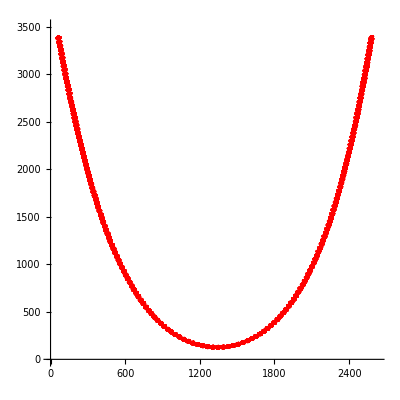

```mathematica
"■"; chainPos=PixelValuePositions[imD,1];
ListPlot[chainPos,PlotRange->{{0,nx},{0,ny}},PlotStyle->Red,AspectRatio->1,ImageSize->400]
```

Note again that the total number of data points (red) describing the chain is large:

```mathematica
"■"; Length[chainPos]
```

186322

Lets try fitting a parabola (quadratic) as proposed by Galileo:

```mathematica
"■"; fn[x_,a0_,a1_,a2_]:=a0+a1 x+a2 x^2;
nlm=NonlinearModelFit[chainPos,fn[x,a0,a1,a2],{a0,a1,a2},x]
{aa0,aa1,aa2}={a0,a1,a2}/.nlm["BestFitParameters"];
```

2
FittedModel[<|Type -> Nonlinear, Model -> <|FittedParameterRules -> {a0 -> 3524.48, a1 -> -5.4665, a2 -> 0.00205675}, IndependentVariables -> {x}, FitExpression -> a0 + a1 x + a2 x , ParameterConstraints -> True|>, KeyNames -> Automatic, Weights -> <|Exa<<8>>hts -> 1|>, «1», Localizer -> Function[Null, FittedModels`LocalizedBlock[{a0, a1, a2, x}, #1], {HoldAll}], Options -> {}|>]

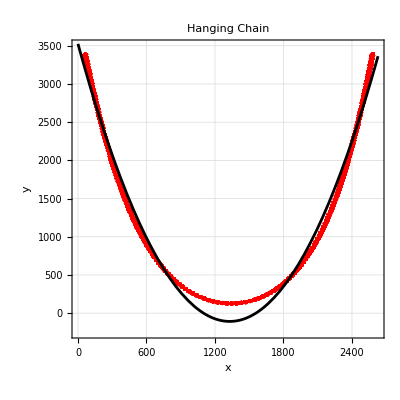

```mathematica
"■"; Show[
ListPlot[chainPos,PlotRange->{{0,nx},{-250,ny}},PlotStyle->Red,PlotTheme->"Detailed",FrameLabel->{"x","y"},LabelStyle->{12,Black},PlotLabel->"Hanging Chain",AspectRatio->1,ImageSize->400],
Plot[fn[x,aa0,aa1,aa2],{x,0,nx},PlotStyle->Black]]
```

Clearly the best fit quadratic is not a great fit.

#### Catenary

The equation of a simple catenary is:

```mathematica
"■"; fn[x_]:=(ⅇ^x+ⅇ^-x)/2
```

This is otherwise known as the cosh function. Lets plot them together:

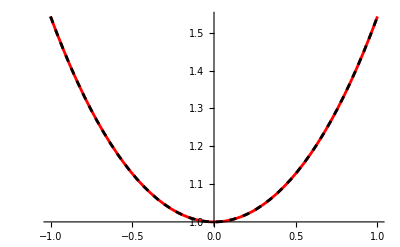

```mathematica
"■"; Plot[{fn[x],Cosh[x]},{x,-1,1},PlotStyle->{Red,{Black, Dashed}}]
```

A scaling parameter, α, is usually added to accommodate different lengths of chain and different spacing between the two points holding the ends of the chain. This parameter can be also subtracted to force the lowest vertical position of the chain to be 1 :

```mathematica
"■"; fn[x_,α_]:=α(ⅇ^(x/α)+ⅇ^(-x/α))/2-α
```

```mathematica
"■"; Manipulate[
Plot[{fn[x,α],Cosh[x]},{x,-5,5},PlotRange->{{-5,5},{-0.1,5}},PlotStyle->{Red,Black},Frame->True,FrameLabel->{"x","y"},LabelStyle->{12,Black},GridLines->Automatic,PlotLabel->"Scaled Catenary and Unscaled Cosh Functions",AspectRatio->0.8,ImageSize->400],
{{α,1},0.1,4,Appearance->"Labeled"},ControlPlacement->Top]
```

When a catenary is measured there will usually be an offset in both x and y. We can therefore include two extra parameters, x0 and y0, to represent this offset:

```mathematica
"■"; fn[x_,α_,x0_,y0_]:=α(ⅇ^((x-x0)/α)+ⅇ^((-(x-x0))/α))/2+y0-α
```

```mathematica
"■"; Manipulate[Show[
ListPlot[chainPos,PlotRange->{{0,nx},{-250,ny}},PlotStyle->Red,PlotTheme->"Detailed",Frame->True,FrameLabel->{"x","y"},LabelStyle->{12,Black},PlotLabel->"Hanging Chain",AspectRatio->1,ImageSize->400],
Plot[fn[x,α,x0,y0],{x,0,nx},PlotStyle->Black]],
{{α,300},100,1000,Appearance->"Labeled"},
{{x0,1300},1100,1500,Appearance->"Labeled"},
{{y0,0},0,500,Appearance->"Labeled"},
ControlPlacement->Top]
```

General::prng: The value of the option PlotRange -> {{0, nx}, {-250, ny}}
     is not All, Full, Automatic, a positive machine number or an appropriate
     list of range specifications.

ListPlot::lpn: chainPos is not a list of numbers or pairs of numbers.

Plot::plln: Limiting value nx in {x, 0, nx}
     is not a machine-sized real number.

Show::gcomb: Could not combine the graphics objects in 
    Show[ListPlot[chainPos, PlotRange -> {{0, nx}, {-250, ny}}, 
      PlotStyle -> RGBColor[1, 0, 0], PlotTheme -> Detailed, Frame -> True, 
      <<3>>, AspectRatio -> 1, ImageSize -> 400], Plot[<<3>>]].

Lets now use a nonlinear minimization algorithm to fit the three parameters automatically:

```mathematica
"■"; αα=450; xx0=1300; yy0=250;
nlm=NonlinearModelFit[chainPos,fn[x,α,x0,y0],{{α,αα},{x0,xx0},{y0,yy0}},x,Method->"LevenbergMarquardt"]
{αα,xx0,yy0}={α,x0,y0}/.nlm["BestFitParameters"]
```

-((x - x0)/α)    (x - x0)/α
                                                                                                                                                                         (E              + E          ) α
FittedModel[<|Type -> Nonlinear, Model -> <|FittedParameterRules -> {α -> 448.064, x0 -> 1327.15, y0 -> 145.115}, IndependentVariables -> {x}, FitExpression -> y0 - α + --------------------------------, ParameterConstraints -> True|>, KeyNames -> Automatic, «2», Localizer -> Function[Null, FittedModels`LocalizedBlock[{x, x0, y0, α}, #1], {HoldAll}], Options -> {}|>]
                                                                                                                                                                                        2

{448.064,1327.15,145.115}

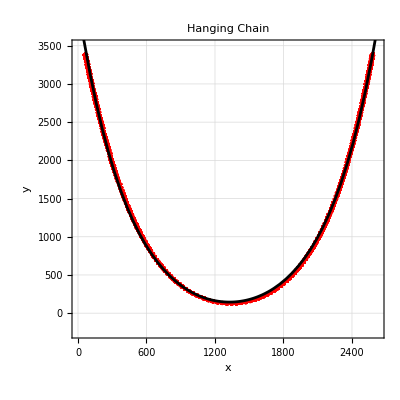

```mathematica
"■";Show[
ListPlot[chainPos,PlotRange->{{0,nx},{-250,ny}},PlotStyle->Red,PlotTheme->"Detailed",Frame->True,FrameLabel->{"x","y"},LabelStyle->{12,Black},PlotLabel->"Hanging Chain",AspectRatio->1,ImageSize->400],
Plot[fn[x,αα,xx0,yy0],{x,0,nx},PlotStyle->Black]]
```

This is a good fit but we could do a bit better. It could be that the camera (which was hand held) should have been better aligned vertically.

#### Rotate Image

The image of the chain was taken by hand using an unmounted mobile phone. Although an attempt was made to align the camera with what was perceived as the vertical axis it is clear from the data above that a slight clockwise rotation of the chain image might help. Mathematica provides an image rotation function called ImageRotate[] we can use for this. After experimenting with a few different amounts of image rotation I settled on a -0.4 deg rotation:

```mathematica
"■"; imDR=ImageRotate[imD,-0.4 (2 π)/360,Background->Black]; (* 1 deg is (2 π)/360 radians *)
```

We will now thin this rotated image:

```mathematica
"■"; imRT=Thinning[imDR];
chainPos=PixelValuePositions[imRT,1];
```

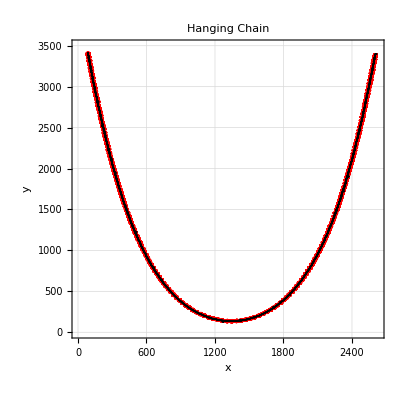

```mathematica
"■"; Show[
ListPlot[{PixelValuePositions[imDR,1],chainPos},PlotRange->{{0,nx},{0,ny}},PlotStyle->{Red,Black},PlotTheme->"Detailed",Frame->True,FrameLabel->{"x","y"},LabelStyle->{12,Black},PlotLabel->"Hanging Chain",AspectRatio->1,ImageSize->400]]
```

We can see that the thinned data fall inside the original data.

Lets now fit the catenary to the thinned data:

```mathematica
"■"; nlm=NonlinearModelFit[chainPos,fn[x,α,x0,y0],{{α,αα},{x0,xx0},{y0,yy0}},x,Method->"LevenbergMarquardt"];
{αα,xx0,yy0}={α,x0,y0}/.nlm["BestFitParameters"];
```

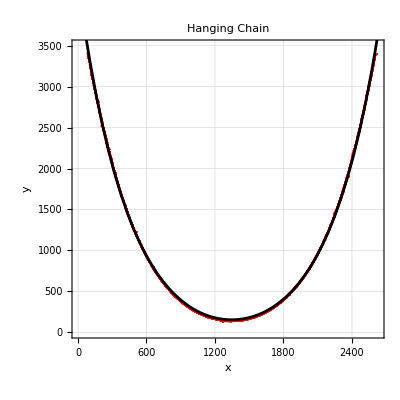

```mathematica
"■"; Show[
ListPlot[chainPos,PlotRange->{{0,nx},{0,ny}},PlotStyle->Red,PlotTheme->"Detailed",Frame->True,FrameLabel->{"x","y"},LabelStyle->{12,Black},PlotLabel->"Hanging Chain",AspectRatio->1,ImageSize->400],
Plot[fn[x,αα,xx0,yy0],{x,0,nx},PlotStyle->Black]]
```

Clearly a great fit.

#### Parameter Sensitivity Functions

Lets compute the three parameter sensitivity functions. We need to explicitly define the least squares objective function which was used within the NonlinearModelFit[] function used above:

```mathematica
"■"; rmsError1[α_,x0_,y0_]:=With[{x=chainPos[[All,1]],y=chainPos[[All,2]]},
RootMeanSquare[y-fn[x,α,x0,y0]]]
rmsError1[αα,xx0,yy0]
```

17.6073

The best fit parameters obtained above are:

```mathematica
"■"; {αα,xx0,yy0}
```

{447.349,1345.85,152.808}

We now hold 2 of the parameters fixed at their least squares (optimum) values while the third is varied about it optimum value:

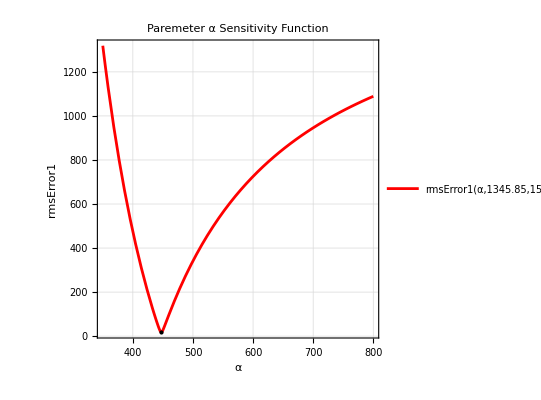

```mathematica
"■"; Plot[rmsError1[α,xx0,yy0],{α,350,800},PlotRange->All,PlotStyle->Red,PlotTheme->"Detailed",Frame->True,FrameLabel->{"α","rmsError1"},LabelStyle->{12,Black},
Epilog->Point[{αα,rmsError1[αα,xx0,yy0]}],PlotLabel->"Paremeter α Sensitivity Function",AspectRatio->1,ImageSize->400]
```

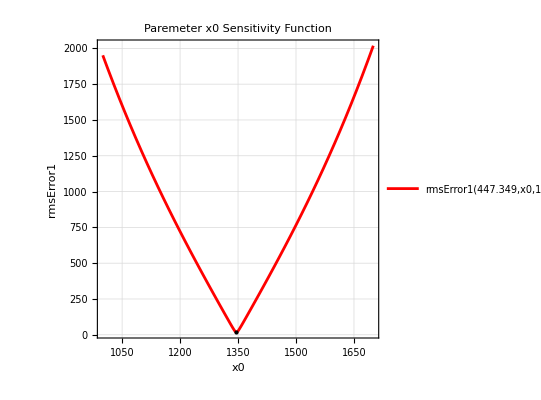

```mathematica
"■"; Plot[rmsError1[αα,x0,yy0],{x0,1000,1700},PlotRange->All,PlotStyle->Red,PlotTheme->"Detailed",Frame->True,FrameLabel->{"x0","rmsError1"},LabelStyle->{12,Black},
Epilog->Point[{xx0,rmsError1[αα,xx0,yy0]}],PlotLabel->"Paremeter x0 Sensitivity Function",AspectRatio->1,ImageSize->400]
```

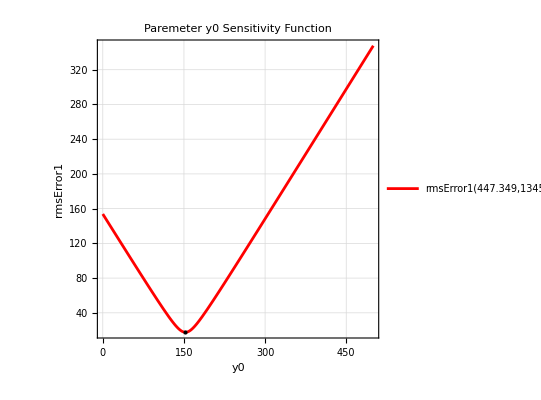

```mathematica
"■"; Plot[rmsError1[αα,xx0,y0],{y0,0,500},PlotRange->All,PlotStyle->Red,Frame->True,PlotTheme->"Detailed",FrameLabel->{"y0","rmsError1"},LabelStyle->{12,Black},
Epilog->Point[{yy0,rmsError1[αα,xx0,yy0]}],PlotLabel->"Paremeter y0 Sensitivity Function",AspectRatio->1,ImageSize->400]
```

These three parameter sensitivity functions are nice and “deep” indicating that all three parameters are important to the fit.

#### A better approach

We now consider the problem of estimating the three parameters, a, x0 and y0. We might take the usual approach and use a nonlinear minimization technique to estimate the values of the three parameters which minimize the sum of squared difference between the measured yData and the predicted y values. Such an objective function would look like:

```mathematica
"■";rmsError1[α_,x0_,y0_]:=With[{x=chainPos[[All,1]],y=chainPos[[All,2]]},
RootMeanSquare[y-fn[x,α,x0,y0]]]
```

The optimal parameters obtained using the traditional least squares objective function (i.e., from NonlinearModelFit[]) were:

```mathematica
"■";{αα,xx0,yy0}
```

{447.349,1345.85,152.808}

Lets check what rmsError1 these parameters give:

```mathematica
"■";rmsError1[αα,xx0,yy0]
```

17.6073

Notice how quickly rmsError1 was determined.

It has been called rmsError1[ ]  to distinguish it from a much more computationally involved objective function denoted rmsError2[ ] below.

rmsError1[ ] is the objective function used by the nonlinear minimization algorithm, NonlinearModelFit[], to fit the catenary function above. The problem with this approach is that we are effectively assuming that all the measurement error is in the y axis measurements. This is not a valid assumption here as the x axis measurements probably have about the same error as the y axis measurements. We are therefore faced with the problem of fitting a nonlinear equation to a data set having equal measurement error in both axes.

If the measurement errors are assumed to be Gaussian distributed and independent (i.e. white) then we want to find the parameters which minimize the sum of squared perpendicular distances between the measured data points and the function. This is sometimes called “Total Least Squares”, “Perpendicular Regression”, “Orthogonal Regression” or “Deming Regression” (when fitting a straight line). This is not nearly as straight forward, is computationally intensive and indeed is rarely undertaken. 

The distance between the function, f(x), and a measured data point  (xi, yi) is:

```mathematica
"■"; distance[x_,xi_,yi_,α_,x0_,y0_]:=√((x-xi)^2+(fn[x,α,x0,y0]-yi)^2)
```

The minimum distance occurs when the line from the data point to the function is normal (perpendicular) to the function tangent line. 

Lets look at what we mean by this:

#### Finding the distance from a point to a function

Imagine that we have a function:

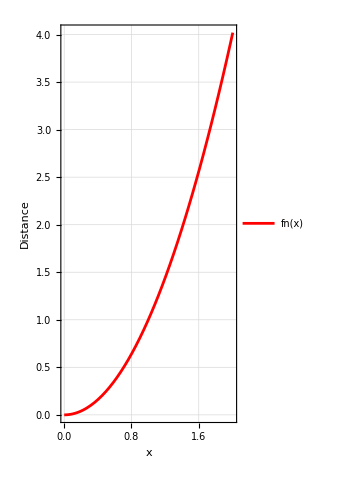

```mathematica
"■"; fn[x_]:=x^2
Plot[fn[x],{x,0,2.2},PlotRange->{{0,2.01},{0,4.02}},PlotStyle->Red,PlotTheme->"Detailed",FrameLabel->{"x","Distance"},LabelStyle->{12,Black},AspectRatio->2,ImageSize->250]
```

Now lets add a point near the function :

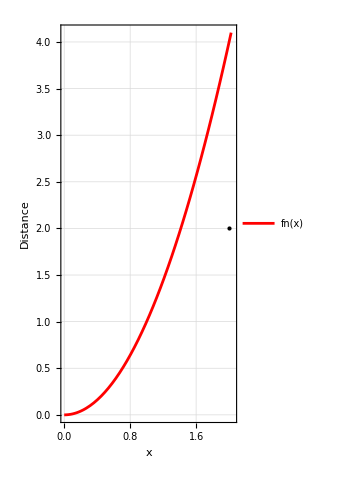

```mathematica
"■"; xi=2; yi=2;
Plot[fn[x],{x,0,2.2},PlotRange->{{0,2.05},{0,4.1}},PlotStyle->Red,PlotTheme->"Detailed",FrameLabel->{"x","Distance"},LabelStyle->{12,Black},AspectRatio->2,ImageSize->250,Epilog->{Black,Point[{xi,yi}]}]
```

We ask how we can find the line from the point to the curve which minimizes the line length (distance). We can always draw another line tangent to the curve which touches the curve:

```mathematica
"■"; Manipulate[Plot[fn[x],{x,0,2},PlotRange->{{0,2.05},{0,4.1}},PlotStyle->Red,PlotTheme->"Detailed",FrameLabel->{"x","Distance"},LabelStyle->{12,Black},AspectRatio->2,ImageSize->250,Epilog->{{Black,Point[{xi,yi}]},{Black,InfiniteLine[{u,fn[u]},{1,fn'[u]}]},{Black,Dotted,Line[{{0,fn[u]},{u,fn[u]}}]},
{Black,Dotted,Line[{{u,0},{u,fn[u]}}]},
{Blue,Line[{{u,fn[u]},{xi,yi}}]}}],
{{u,1.2},1,2,Appearance->"Labeled"},
Dynamic[ThermometerGauge[√((xi-u)^2+(yi-fn[u])^2),{0.5,1.25},AspectRatio->5,ImageSize->90,GaugeLabels->{"Value",Placed["Dist",Top]}]],ControlPlacement->{Top,Right}]
```

Try changing the x axis position of the tangent line (black) to see how small you can make the length of the blue line (distance). Notice that the length of the blue line (i.e. the distance between the point and the black tangent line to the red function) is smallest when the blue line is normal (i.e., 90 deg) to the black tangent line.

The question now becomes how can we automatically determine this minimum distance?
One approach is to compute the slopes of the black tangent line and the blue distance line. These two lines will be orthogonal (normal to each other) when the reciprocal of one slope equals minus the other slope. A root finding algorithm can be used to find the x value at which this equality occurs. However, in practice, this is difficult to get to work reliably because as the slopes go near vertical or horizontal the root finding algorithm fails to converge.

A better alternative is to use a minimization technique to find the value of x on the red function, fn[x],  at which the distance is minimum. If we look at the distance as a function of x we can see that there is a clear minimum:

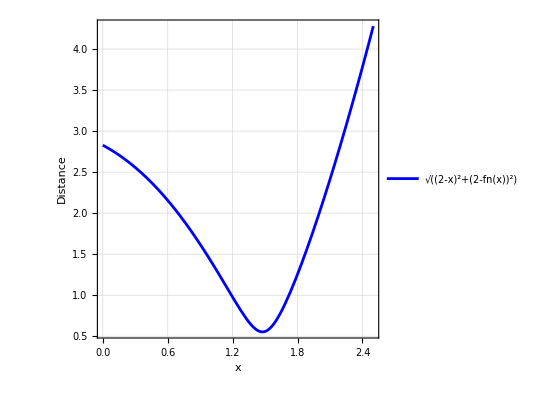

```mathematica
"■"; Plot[√((xi-x)^2+(yi-fn[x])^2),{x,0,2.5},PlotStyle->Blue,PlotTheme->"Detailed",FrameLabel->{"x","Distance"},LabelStyle->{12,Black},AspectRatio->1,ImageSize->400]
```

We just need an algorithm which finds this minimum for us. We can use Mathematica’s FindMinimum[ ] for this. Note that we constrain the search to a region given by  (xi - 1) ≤ x ≤ (xi + 1):

```mathematica
"■"; xMin=x/.Last[FindMinimum[{(xi-x)^2+(yi-fn[x])^2,(xi-1)≤x≤(xi+1)},x]]
```

1.47569

Notice above that we used distance^2 rather than distance. This is because the square root is less well behaved and slower (see below)

```mathematica
"■"; dist=√((xi-xMin)^2+(yi-fn[xMin])^2)
```

0.553592

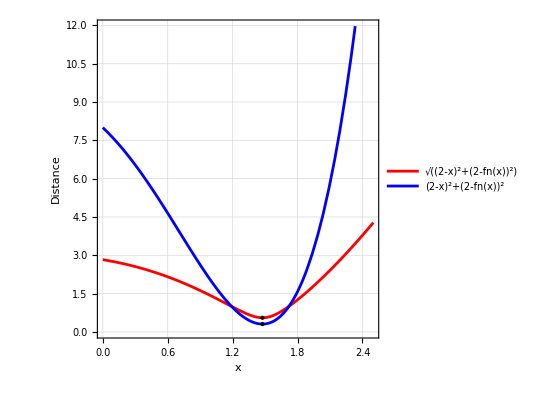

```mathematica
"■"; Plot[{√((xi-x)^2+(yi-fn[x])^2),(xi-x)^2+(yi-fn[x])^2},{x,0,2.5},PlotStyle->{Red,Blue},PlotTheme->"Detailed",FrameLabel->{"x","Distance"},LabelStyle->{12,Black},AspectRatio->1,ImageSize->400,Epilog->{{PointSize[Medium],Point[{xMin,dist}]},{PointSize[Medium],Point[{xMin,dist^2}]}}]
```

Here we show the distance and distance^2 functions. Note that they have the same x value at their respective minima.
The values of x and distance obtained here (i.e., xx0, and yy0) should be close to the ones you obtained when you tried minimizing the distance by hand above.

#### Fit the Catenary Function to the Chain by Minimizing the Sum of Squared Distances

With the knowledge above we can now set about to fit the Catenary to our chain by minimizing the overall sum of squared perpendicular distances between each data point and the Catenary. Such fitting techniques are known alternatively as orthogonal distance regression (ODR), orthogonal least squares or total least squares.

As mentioned above this is correct approach when we have equal Gaussian, white measurement errors in both x and y measurements.

There is no problem using this objective function when the function to be fitted is linear because there is a direct (non-iterative) solution in this case (see the Wolfram Function Repository function called OrthogonalLineFit[]).  The problem is more challenging when the model is nonlinear.

However if the function to be fitted is nonlinear then usually there is no direct method to determine the sum of perpendicular  squared distances. Usually a minimization technique is used to find the minimum distance between the function and every data point. This has to be repeated for every set of parameters being adjusted during the overall minimization. 

A faster approach is to determine the perpendicular distance via root finding.

#### Fit the Catenary Function to the Chain by Minimizing the Sum of Squared Perpendicular Distances

```mathematica
"■"; 
catenary[x_,a_,x0_,y0_]:=a*Cosh[(x-x0)/a]-y0;
catenaryDerivative[x_,a_,x0_]:=Sinh[(x-x0)/a];
(* Define the perpendicular distance from a point to the catenary *)
perpendicularDistance[{x0Point_,y0Point_},a_?NumericQ,x0_?NumericQ,y0_?NumericQ]:=Module[{xxx,root},(*Use a better initial guess for xxx based on the data*)root=Quiet[Check[FindRoot[(catenary[xxx,a,x0,y0]-y0Point)/(xxx-x0Point)==-(1/catenaryDerivative[xxx,a,x0]),{xxx,x0Point}],{xxx->x0Point}]];(*Fall back to x0Point if FindRoot fails*)Norm[{x0Point,y0Point}-{root[[1,2]],catenary[root[[1,2]],a,x0,y0]}]];
(*Total squared perpendicular distance for all points*)
totalPerpendicularDistance[a_?NumericQ,x0_?NumericQ,y0_?NumericQ]:=Total[Quiet[perpendicularDistance[#,a,x0,y0]^2&/@chainPos]];
```

The parameters estimated from the vertical least squares fit are:

```mathematica
"■"; {αα,xx0,yy0}
```

{447.349,1345.85,152.808}

We will use these as initial estimates for our orthogonal fit. This will take some time depending on your computer speed:

```mathematica
"■"; (* Minimize the total squared perpendicular distance *)
(* Constrain a>0 to avoid division by zero *)
fitResult=Quiet[FindMinimum[{totalPerpendicularDistance[a,x0,y0],a>0},{{a,αα},{x0,xx0},{y0,yy0}}]];
```

```mathematica
"■"; (* Extract the fitted parameters *)
{aFit,x0Fit,y0Fit}={a,x0,y0}/. fitResult[[2]]
```

{447.349,1345.85,294.541}

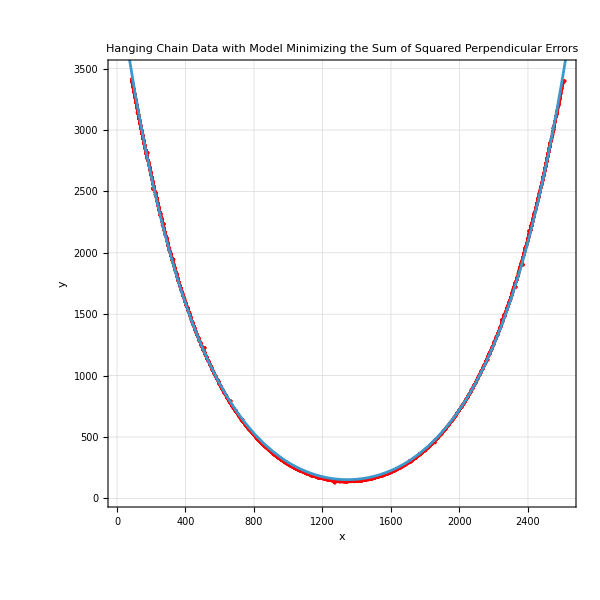

```mathematica
"■"; Show[
ListPlot[chainPos,PlotRange->{{0,nx},{0,ny}},PlotStyle->Red,PlotTheme->"Detailed",Frame->True,FrameLabel->{"x","y"},LabelStyle->{12,Black},PlotLabel->"Hanging Chain Data with Model Minimizing the Sum of Squared Perpendicular Errors",AspectRatio->1,ImageSize->600],
Plot[catenary[x,aFit,x0Fit,y0Fit],{x,0,nx}]]
```

As you can see the bottom of the chain could be a bit better fitted but otherwise a really good fit.
An alternative but more involved approach would be to focus more on the fit near the bottom of the catenary. This would involve what is called weighted orthogonal least squares fitting where each data point is weighted and the where the data points near the bottom of the catenary would be given larger weights than those higher up.